82.5

248

357.5

3431.37

1600.07

2335.26

{{R_x→-637.119-3035.84 Cos[θ_p],R_z→1366.31+3035.84 Sin[θ_p],R_(2 x)→-962.951+700.578 Cos[θ_p],R_(2 z)→2065.06-700.578 Sin[θ_p]}}

{-637.119-3035.84 Cos[θ_p]}

{1366.31+3035.84 Sin[θ_p]}

{-962.951+700.578 Cos[θ_p]}

{2065.06-700.578 Sin[θ_p]}

{√((-637.119-3035.84 Cos[θ_p])^2+(1366.31+3035.84 Sin[θ_p])^2)}

{√((-962.951+700.578 Cos[θ_p])^2+(2065.06-700.578 Sin[θ_p])^2)}

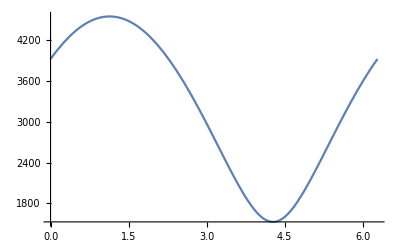

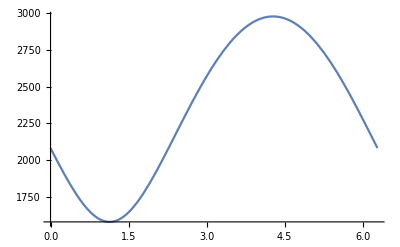

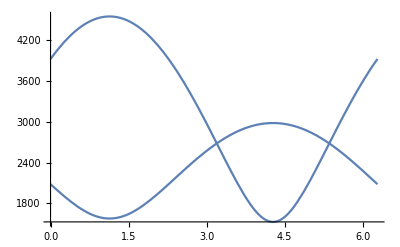

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ_p→-3.08828},{θ_p→-0.925977}}

```mathematica
(*Primer eje, a b y c son las distancias a los rodamientos y a la rueda dentada*)
d1=82.5 (*dist al primer rodamiento*)
d2=248 (*dist a la rueda dentada*)
d3=357.5 (*dist al segundo rodamiento*)
Wt=3431.37 (*fuerza en el engranaje*)
Wr=1600.07
Fp=2335.26(*fuerza en la polea*)
sol=Solve[{Subscript[R, 1z]+Subscript[R, 2z]-Wt-Fp Sin[Subscript[θ, p]]==0, Subscript[R, 1x]+Subscript[R, 2x]+Wr+Fp Cos[Subscript[θ, p]]==0, -Subscript[R, 1x]d1-Wr d2-Subscript[R, 2x] d3==0, Subscript[R, 1z] d1-Wt d2+Subscript[R, 2z] d3==0}, {Subscript[R, 1x], Subscript[R, 1z], Subscript[R, 2x], Subscript[R, 2z]}]
R1x=sol[[All,1,2]]
R1z=sol[[All,2,2]]
R2x=sol[[All,3,2]]
R2z=sol[[All,4,2]]
Subscript[R, 1]=√(R1x^2+R1z^2)
Subscript[R, 2]=√(R2x^2+R2z^2)
p1=Plot[Subscript[R, 1], {Subscript[θ, p],0, 2π}]
p2=Plot[Subscript[R, 2], {Subscript[θ, p],0, 2π}]
Show[p1,p2] (*aca estoy mostrando las reacciones en función del ángulo de la polea*)
Solve[Subscript[R, 1]==Subscript[R, 2], Subscript[θ, p]](* cuando las reacciones son iguales estoy minimizando ambas fuerzas al mismo tiempo, esto me permite tener un eje mas chico en general*)
```